Sapphire
Q^-1vsb

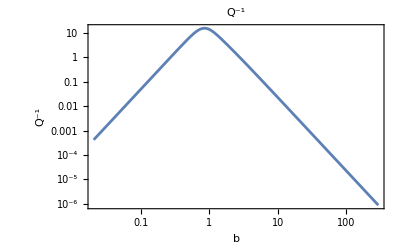

```mathematica
QwoHeatFlow =δE*Abs[ 6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) ]/.
{δE->32,ξ->1.43 b^(3/2)};
QHeatFlowg=LogLogPlot[QwoHeatFlow,{b,0.02,300},PlotLabel->"Q^-1", Frame->True,FrameLabel->{b,"Q^-1"}]
```

```mathematica
QHeatFlow=δE*Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.{δE->32,ξ->1.43 b^(3/2)}; (*sapphire*)
```

d=1.1,1.3,1.7

8.20735 Abs[1/(b^(9/2) (Cos[3.146 b^(3/2)]+Cosh[3.146 b^(3/2)]))(-2.86 b^(3/2) (Cos[3.003 b^(3/2)] Cosh[0.143 b^(3/2)]+Cos[0.143 b^(3/2)] Cosh[3.003 b^(3/2)])-Cosh[3.003 b^(3/2)] Sin[0.143 b^(3/2)]+Cosh[0.143 b^(3/2)] Sin[3.003 b^(3/2)]-Cos[3.003 b^(3/2)] Sinh[0.143 b^(3/2)]+Cos[0.143 b^(3/2)] Sinh[3.003 b^(3/2)])]

8.20735 Abs[1/(b^(9/2) (Cos[3.718 b^(3/2)]+Cosh[3.718 b^(3/2)]))(-2.86 b^(3/2) (Cos[3.289 b^(3/2)] Cosh[0.429 b^(3/2)]+Cos[0.429 b^(3/2)] Cosh[3.289 b^(3/2)])-Cosh[3.289 b^(3/2)] Sin[0.429 b^(3/2)]+Cosh[0.429 b^(3/2)] Sin[3.289 b^(3/2)]-Cos[3.289 b^(3/2)] Sinh[0.429 b^(3/2)]+Cos[0.429 b^(3/2)] Sinh[3.289 b^(3/2)])]

8.20735 Abs[1/(b^(9/2) (Cos[4.862 b^(3/2)]+Cosh[4.862 b^(3/2)]))(-2.86 b^(3/2) (Cos[3.861 b^(3/2)] Cosh[1.001 b^(3/2)]+Cos[1.001 b^(3/2)] Cosh[3.861 b^(3/2)])-Cosh[3.861 b^(3/2)] Sin[1.001 b^(3/2)]+Cosh[1.001 b^(3/2)] Sin[3.861 b^(3/2)]-Cos[3.861 b^(3/2)] Sinh[1.001 b^(3/2)]+Cos[1.001 b^(3/2)] Sinh[3.861 b^(3/2)])]

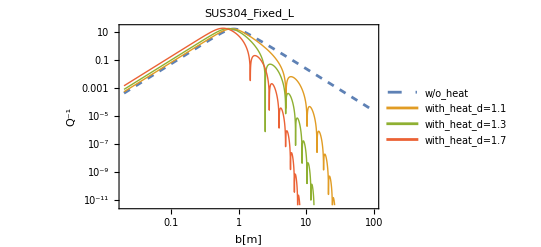

```mathematica
Q11=QHeatFlow/.{d->1.1}
Q13=QHeatFlow/.{d->1.3}
Q17=QHeatFlow/.{d->1.7}
HeatFlowg=LogLogPlot[{QwoHeatFlow,Q11,Q13,Q17},{b,0.02,100},PlotLabel->"SUS304_Fixed_L", Frame->True,FrameLabel->{"b[m]","Q^-1"},PlotStyle->{Dashed,Thick,Thick,Thick},PlotLegends->Placed[{"w/o_heat","with_heat_d=1.1","with_heat_d=1.3","with_heat_d=1.7"},{0.3,0.25}],GridLinesStyle->LightGray,GridLines->Full]
```